```mathematica
ex4 = Import["./Documents/Lab_6_Data_Analysis/exp4-21.csv"]
```

{{Frequency (kHz),Average Voltage,StdEV Voltage,Average Voltage Squared,StdEV Voltage Squared},{20,1.35553,7.97807,1.83745,63.6496},{25,1.65669,10.3093,2.74463,106.282},{30,1.90951,7.93088,3.64624,62.8989},{35,2.14385,7.63549,4.5961,58.3007},{40,2.34241,7.18096,5.48689,51.5662},{45,2.53627,7.591,6.43268,57.6233},{50,2.71594,8.1173,7.37632,65.8906}}

```mathematica
col1 = ex4[[All, 1]][[2 ;; 7]];
col2 = ex4[[All, 2]][[2 ;; 7]];
col3 = ex4[[All, 3]][[2 ;; 7]];
col4 = ex4[[All, 4]][[2 ;; 7]];
col5 = ex4[[All, 5]][[2 ;; 7]]; (*error*)
```

FittedModel[-1.84654+0.183706 x]

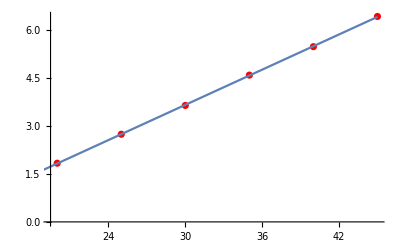
-Graphics-V.b2 (mV).b2Frequency(kHz)

```mathematica
(*Plot Voltage-Squared vs Resistance*)
ex4plotpair = {col1, col4};
ex4plotTuple = Transpose[ex4plotpair];
ListPlot[ex4plotTuple, PlotMarkers->{"O"}];

(*Weighted Least Square Fit*)
sim=Flatten[MapThread[Function[{a},{#1[[1]],a}]/@RandomVariate[NormalDistribution[#1[[2]],#2],200]&,{ex4plotTuple,col5}],1];
fit2=LinearModelFit[ex4plotTuple,x,x,Weights->1/col5]
Labeled[
Show[
ListPlot[ex4plotTuple,PlotStyle->Red],
Plot[{fit2[x]},{x,0,ex4plotTuple[[-1,1]]}]   ],
{"V.b2 (mV).b2", "Frequency(kHz)"},
{Left, Bottom},
RotateLabel->True
]
```

```mathematica
(*Residual Graph*)
```

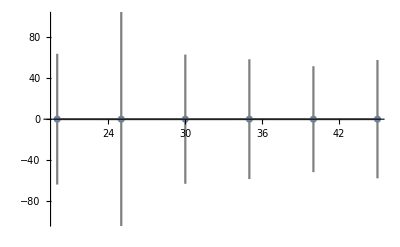
-Graphics-V.b2 (mV).b2Frequency (kHz)

```mathematica
ex4err = Import["./Documents/Lab_6_Data_Analysis/exp4-21_errs.csv"];
col6 = ex4err[[All, 6]][[2 ;; 7]]; (* Predicted Voltage *)
col7 = ex4err[[All, 7]][[2 ;; 7]];   (* Residuals *)                                    

ex4plotpairerrs = {col1, col7};
ex4plotTuplerrs = Transpose[ex4plotpairerrs]; (*x, y*)

ex4plotpairerrs2 = {col1, col7, col5};
ex4plotTuplerrs2= Transpose[ex4plotpairerrs2]; (*x, y, errs*)

Needs["ErrorBarPlots`"]
Labeled[
	Show[
	ListPlot[ex4plotTuplerrs, PlotRange->{-100, 100}],     (*Note the Range*)
	Plot[lm[x],{x,0,12}],
	ErrorListPlot[ex4plotTuplerrs2,PlotStyle->Gray, Joined-> True]
   ],
{"V.b2 (mV).b2", "Frequency (kHz)"},
{Left, Bottom},
RotateLabel->True
]
```